#### paclets

```mathematica
(* code requires prototypes paclet *)
Needs["PacletManager`"];
```

```mathematica
paclet="https://github.com/arnoudbuzing/prototypes/releases/download/v0.5.6/Prototypes-0.5.6.paclet";
```

```mathematica
If[PacletFind["Prototypes"]==={},PacletInstall[paclet]]
```

#### git

```mathematica
git=FileNameJoin[{"C:","Program Files","Git","bin","git"}];
```

```mathematica
repo="git@github.com:CSSEGISandData/COVID-19.git";
```

```mathematica
dir=FileNameJoin[{"D:","git","COVID-19"}];
```

```mathematica
clone[git_,repo_,dir_]:=RunProcess[{git,"clone",repo,dir}]
pull[git_,dir_]:=RunProcess[{git,"-C",dir,"pull"}]
```

```mathematica
If[FileType[dir]===None,clone[git,repo,dir]]
```

```mathematica
If[FileType[dir]===Directory,pull[git,dir]]
```

#### utilities

```mathematica
todate[s_String]:=Module[{d},
Quiet[
d=Check[
DateObject[{s,{"Month","/","Day","/","YearShort"," ","Hour",":","Minute"}}],
Check[
DateObject[{s,{"Year","-","Month","-","Day","T","Hour",":","Minute",":","Second"}}],
$Failed
]
]
]
]
```

```mathematica
import[file_]:=Module[{csv},
csv=Import[file,"CSV"];
csv=csv[[All,1;;6]];
Dataset[
Map[<|
"date"->Interpreter["StructuredDate",DateFormat->{"Month","-","Day","-","Year"}][FileBaseName[file]],
"division"->Interpreter["AdministrativeDivision"][First[#]<>", "<>Second[#]]/.{_Failure->Missing["NotAvailable"]},
"country"->Interpreter["Country"][Second[#]]/.{_Failure->Missing["NotAvailable"]},
"updated"->todate[Third[#]]/.{""->Missing["NotAvailable"]},
"cases"->Fourth[#]/.{""->0},
"deaths"->Fifth[#]/.{""->0},
"recovered"->Sixth[#]/.{""->0}
|>&,
Rest[csv]
]
]
]
```

```mathematica
tsplot[country_]:=Module[{ts},
ts=TimeSeries[N[Normal[ds[Select[#country===country&]][All,{#date,#cases}&]]]];
DateListPlot[ts,
PlotLabel->country["Name"],
PlotRange->{{{2020,1,22},{2020,3,1}},All},
Filling->Axis,
PlotRangePadding->None,
GridLines->Automatic,
DateTicksFormat->{"MonthNameShort"," ","Day"},
FrameTicks->{{Automatic,Automatic},{DateRange[DateObject[{2020,1,22}],DateObject[{2020,3,1}],Quantity[10,"Days"]],Automatic}}
]
]
```

```mathematica
DateRange[DateObject[{2020,1,22}],DateObject[{2020,3,2}],Quantity[1,"Weeks"]]
```

{Day: Wed 22 Jan 2020,Day: Wed 29 Jan 2020,Day: Wed 5 Feb 2020,Day: Wed 12 Feb 2020,Day: Wed 19 Feb 2020,Day: Wed 26 Feb 2020}

#### analysis

```mathematica
path=FileNameJoin[{dir,"csse_covid_19_data","csse_covid_19_daily_reports"}];
```

```mathematica
dailies=FileNames["*.csv",path];
```

```mathematica
datasets=import/@dailies;
```

```mathematica
ds=Join@@datasets;
```

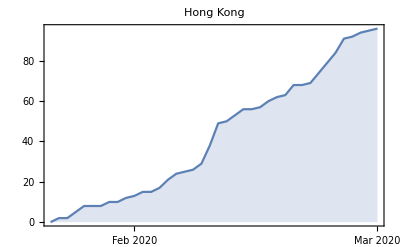

```mathematica
tsplot[Entity["Country","HongKong"]]
```

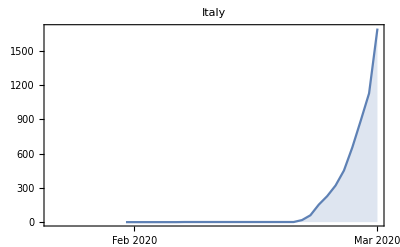

```mathematica
tsplot[Entity["Country","Italy"]]
```

```mathematica
countries=DeleteMissing[ds[Union,"country"]];
```

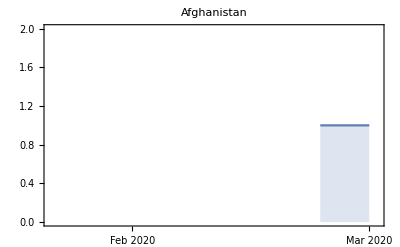
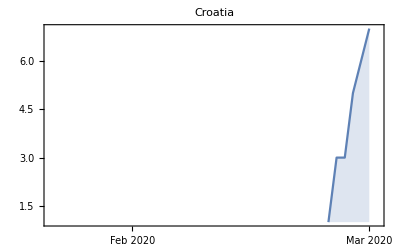
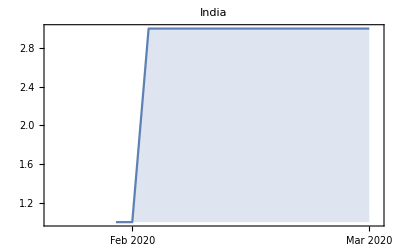
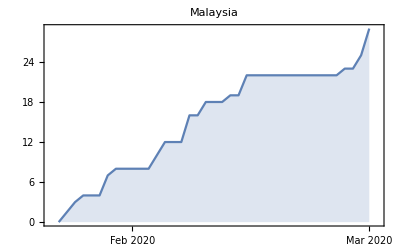
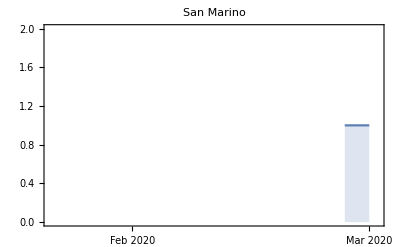
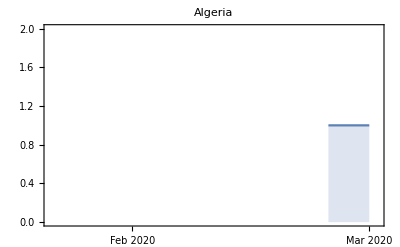
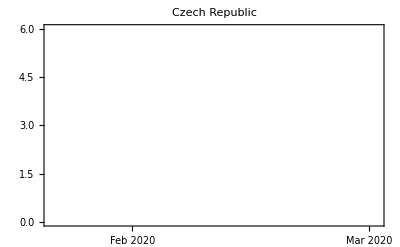
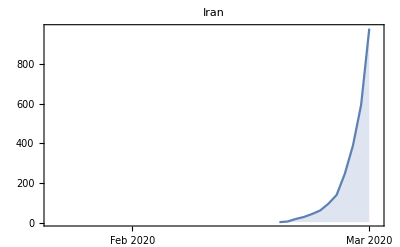
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- |

```mathematica
Multicolumn[tsplot/@Normal[countries],5]
```

```mathematica
TimeSeries[KeyValueMap[List,Normal[ds[GroupBy[#date&],Total[#[[All,5]]]&]]]]
```

```mathematica
DateListPlot[%]
```

```mathematica
ts2=ds[GroupBy[#division&],TimeSeries[Map[{#["date"],#["cases"]}&,#]]&]
```

```mathematica
ts2[KeySelect[Not[MissingQ[#]]&]]
```

```mathematica
DateListPlot[ts2[KeySelect[Not[MissingQ[#]]&]],PlotRange->All]
```

```mathematica
ts3=ds[GroupBy[#country&],TimeSeries[Map[{#["date"],#["cases"]}&,#]]&];
```

```mathematica
DateListPlot[ts3[KeySelect[Not[MissingQ[#]]&]],PlotRange->All]
```

```mathematica
StackedDateListPlot[ts3[KeySelect[Not[MissingQ[#]]&]]]
```